## Homework 5

## Exercise 1

(-a_r | 0
-l_(Π+r) | 1) (dr
dm) =(a_f df-dy
l_(Π+r)dΠ+l_y dy)

b^-1== (-1/a_r | 0
-(l_(r+Π))/a_r | 1)
(dr
dm) == (-1/a_r | 0
-(l_(r+Π))/a_r | 1) (a_f df-dy
l_(Π+r)dΠ+l_y dy)
(dr
dm) == ((dy-df a_f)/a_r
dy l_y+((dy-df a_f+dΠ a_r) l_(r+Π))/a_r)
We can  find  dr/df by dividing the first row of the matrix by df.

## Exercise 2

Maximize x y s.t. p_x x + p_y y = 100
ℒ = x y + λ (p_x x + p_y y - 100)
(∂ℒ)/(∂x) = y + λ p_x = 0
(∂ℒ)/(∂y) = x + λ p_y = 0 
(∂ℒ)/(∂λ) = p_x x + p_y y - 100 = 0

```mathematica
l = x y + λ(px x + py y - 100)
lx = D[l, x] == 0
ly = D[l, y] == 0
ll = D[l, λ] == 0
soln = Solve[{lx, ly, ll}, {x, y, λ}]
```

x y+(-100+px x+py y) λ

y+px λ==0

x+py λ==0

-100+px x+py y==0

{{x→50/px,y→50/py,λ→-50/(px py)}}

The elasticity of the functions are:

## Exercise 3

Corbae 2.5.3

We write the relations in matrix form for convenience:

The ≤ relation) on the set {0, 1, 2, 3,4}:
(1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1)
We can see that the matrix is upper traingular.  For every element in {0, 1, 2, 3,4} either aRb or bRa. We also see that the diagonals are all 1, therefore it is reflexive.

The = relation on {0, 1, 2, 3, 4}:
(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)
We can see that this relation is not complete because (for example) neither (0, 1) nor (1, 0) are in the set of =.  This relationship is transitive because it is only defined for elements for identical elements.

The < relation on {0, 1, 2, 3, 4}:
(0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)
This relation is not complete because (0, 0) is not in the set of >.
The relation is transitive because for any aRb ∧ bRc ⇒ aRc (we can see this in the matrix representation, where all elements to the right of the first “1” in a row are also 1.
(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

We can see the relation is not complete because elements such as (0, 0) are not in the set of ≠.  We can see the set is not transitive because 3 ≠ 1, 1 ≠ 3 does not imply 3 ≠ 3 (that is, (1,3) and (3, 1) are in the set of the relation ≠, but (1, 1) is not).

## Exercise 4

P 72
1 a. Negate “Everyone who is majoring in math has a friend who needs help with his homework.”
Let A be the set of people majoring in math
Let B be the set of people who need help with homework
Let xFy be the relation x and y are friends
We can write the above symbolically as
∀_x ∈ A ∃_y ∈ B ∧ (x, y) ∈ F
Negating this:
¬(∀_x ∈ A ∃_y ∈ B such that (x, y) ∈ F)
⧦ (∃_x ∈ A ¬ (∃_y ∈ B such that (x,y) ∈ F)
⧦ (∃_x ∈ A such that ∀_y ∈ B ¬(x, y) ∈ F)
⧦ (∃_x ∈ such that A ∀_y ∈ B ¬(x, y) ∉ F)

Which we can rewrite this as “there is someone who is majoring in math who doesn’t have any friends who needs help with math”. 
1 b. Negate “Everyone has a roommate who dislikes everyone.”
Let xDy be the relation x dislikes y
Let xRy be the relation x and y are roommates
We can rewrite the above statement symbolically as:
∀_x ∃_y s.t. (x,y) ∈ R ∧ (x,y) ∈ D
¬(∀_x ∃_y s.t. (x,y) ∈ R ∧ (x,y) ∈ D)
(∃_x ¬(∃_y s.t. (x,y) ∈ R ∧ (x,y) ∈ D))
(∃_x s.t. (∀_y ¬((x,y) ∈ R ∧ (x,y) ∈ D)))
(∃_x s.t. (∀_y (¬(x,y) ∈ R ∨ ¬(x,y) ∈ D)))
(∃_x s.t. (∀_y ((x,y) ∈ R ∨ (x,y) ∈ D)))
There is someone who has a roommate who doesn’t dislike everyone.

1 c.
Negate A ∪ B ⊆ C \ D
¬(A ∪ B ⊆ C \ D)
⧦¬A ∩ ¬ B ⊆ C \D)
⧦¬A∩B⊈(C\D)

1 d.
Negate ∃_x ∀_y [y > x ⇒ ∃_z (z^2 + 5 z = y)
∀_x ∃_y [y > x ⇒ ∀_z (z^2 + 5 z ≠ y)

2.
a. There is someone in the freshman class who doesn’t have a roommate.
Everyone in the freshman class has a roommate

b. Everyone likes someone, but no one likes everyone
There is someone who doesn’t like anyone or there is someone who likes everyone

c. ∀_a ∈ A ∃_b ∈ B (a ∈ C ⇔ b ∈ C)
∃_a ∈ A ∀_b ∈ B ¬(a ∈ C ⇔ b ∈ C)
∃_a ∈ A ∀_b ∈ B (a ∈ C ∧ b ∉ C) ∨ (a ∉ C ∧ b ∈ C)

d. ∀_y > 0 ∃_x(a x^2 + b x + c = y)
∃_x > 0 ∀_x (a x^2 + b x + c ≠ y)

3.
a. False.
Consider the number 2
There are no a, b, c in the natural number ℕ = {1, 2, 3...} such that a^2 + b^2+c^2 = 2 (however, the statement is false if 0 is in the natural numbers).

b. False
E_(!x) (x - 4)^2 = 9
(x - 4)^2 - 9 = 0
x == 1 || x == 7

c. ∃_(!x) (x - 4)^2 = 25
False, x = 1 or x = 9

d. True. From previous example, if x = 1 and y = 9 then (x - 4)^2 = 25 and (y - 4)^2 = 25

4. Prove ¬∀_xP(x)⧦∃_x¬P(x)
¬∃_xP(x)⧦∀_x¬P(x)
negate both side
¬(¬∃_xP(x))⧦¬(∀_x¬P(x))
distribute
Ε_x¬P(x) ⧦ (¬A_xP(x))

5. ¬E_x∈A P(x)⧦∀_x¬P(x)
by quantifier negation law

P. 170
4.
A = {1, 2, 3}
B = {1, 4}
C = {3, 4}
D = {5}
B ∪ C = {1, 3, 4}
B ∩ C = {4}
A ∪ C = {1, 2, 3, 4}
A ∩ C = {3}
B ∪ D = {1, 4, 5}
B ∩ D = {}
A × B = {(1, 1), (1, 4), {2, 1), (2, 4), (3, 1), (3, 4)}
A x C = {(1, 3), (1, 4), (2,3), (2, 4), (3, 3), (3, 4)}
C × D = {(3, 5), (4, 5)}
 
 A × (B ∩ C) = (A × B) ∩ (A × C)
 {1, 2, 3} × {4} = {(1, 1), (1, 4), {2, 1), (2, 4), (3, 1), (3, 4)} ∩ {(1, 3), (1, 4), (2,3), (2, 4), (3, 3), (3, 4)}
 {(1, 4), (2, 4), (3, 4)} = {(1,4), (2, 4), (3, 4)}
 
  A × (B ∪ C) = (A × B) ∪ (A × C)
   {1, 2, 3} × {1, 3, 4} = {(1, 1), (1, 4), {2, 1), (2, 4), (3, 1), (3, 4)} ∪  {(1, 3), (1, 4), (2,3), (2, 4), (3, 3), (3, 4)}
   {(1, 1), (1, 3), (1, 4), (2, 1), (2, 3), (2, 4), (3, 1), (3, 3), (3, 4)} =  {(1, 1), (1, 3), (1, 4), {2, 1), (2,3), (2, 4), (3, 1), (3, 3), (3, 4)}
   
   (A × B) ∩ ( C × D) = (A ∩ C) × (B ∩ D)
   {(1, 1), (1, 4), {2, 1), (2, 4), (3, 1), (3, 4)} ∩ {(3, 5), (4, 5)} = {3} ∩ {}
   {} = {}
   
   (A × B) ∪ (C × D) ⊆ (A ∪ C) × (B ∪ D)
   {(1, 1), (1, 4), {2, 1), (2, 4), (3, 1), (3, 4)} ∪ {(3, 5), (4, 5)} ⊆ {1, 2, 3, 4} ×  {1, 4, 5}
   {(1, 1), (1, 4), {2, 1), (2, 4), (3, 1), (3, 4), (3, 5), (4, 5)} ⊆ {(1, 1), (1, 4), (1, 5), (2, 1), (2, 4), (2, 4), (3, 1), (3, 4), (3, 5), (4, 1), (4, 4), (4, 5)}
   
   A × ∅ = ∅ × A = ∅
   {1, 2, 3} × ∅ = ∅
   ∅ × {1, 2, 3} = ∅ (see page 166).
   
   7. If A has m elements and B has n A × B will have m × n elements.
   
   P. 178
   1 a. {(p, q} ∈ P × P | the person p is a parent of the person q}, where P is the set of all living people}
   The domain is the set of all living people.
   The range is the set of all living people with a living parent.
   
   b. {(x, y) ℝ^2|y>x^2}
   The doman is ℝ. The range is all non-negative real numbers. 
   
   2 a.  {(p,q) ∈ P × P |the person p is a brother of the person q} P is the set of all living people.
   The domain is the set of all living people. The range is the set of all living people with a living brother.
   
  b.  {(x, y) ∈ ℝ^2 | y^2 =1−2/(x^2 + 1)}.
  The domain is the set of all real numbers.  the range is -1 < y < 1.

## Exercise 5

The theorem and proof are not correct.  Consider an empty relation (i.e. no two elements of the non-empty set are in the relation). Then R is trasnsitive and symmetric, but not reflexive.  in order to fix the proof, we must add we must add a quantifier condition (that is for every element a in the set, there exists at least one b such that aRb).

## Exercise 6

if relation R is irreflexive than ∀_a¬(aRa).
If relation R is antisymmetric, then ∀_(a, b) (aRb ∧ bRa) ⇒ a = b
Therefore ∀_(a, b) ((aRb ∧ bRa) ⇒ a = b) ∧ ¬(aRa) ⧦ (¬(aRb ∧ bRa) ∨ a = b) ∧ ¬ (aRa) ⧦ (¬aRb ∨ ¬bRa ∨ a = b) ∧ ¬ aRa⧦aRb ⇒ ¬bRa

## Exercise 7

R is symmetric: iff a_ij = 1 then a_ji = 1 in the bolean matrix representation (where a_ij is the i^th row and j^th column of the boolean matrix representation of the relationship).
Asymettric relation: iff a_ij = 1 then a_ji = 0.
If R is complete, then the matrix is triangular.

## Computational Exercise 1

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Original Relation

-Graphics-

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Symmetric Subelation

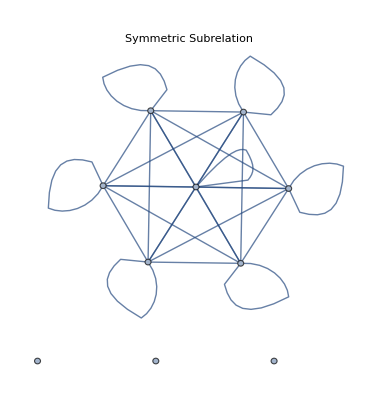

```mathematica
ClearAll[result]
subsym[x_] := Module[{result=Table[Table[0, Length[x]], Length[x]]},
Do[If[x[[i]][[j]] == 1 && x[[j]][[i]] == 1,
result[[i]][[j]] = 1,
0], {i, 1, Length[x]}, {j, 1, Length[x]}];
result
]
x = Table[{1,0,1,1,0,1,1,1,0,1}, 10];
x//Labeled[TableForm[#],"Original Relation"]&
AdjacencyGraph[x, PlotLabel->"Graph of original adjacency matrix"]
s = subsym[x];
s//Labeled[TableForm[#],"Symmetric Subelation"]&
AdjacencyGraph[s, PlotLabel->"Symmetric Subrelation"]
```

## Compuational Exercise 2

```mathematica
adjMatrix = Table[RandomChoice[{0, 1},5], 5]
adjMatrix//Labeled["Adjacency Matrix", TableForm[#]]&
adjGraph = AdjacencyGraph[adjMatrix, PlotLabel->"Adjacency Graph"]
```

{{1,0,1,1,0},{1,1,1,1,0},{0,0,0,1,1},{1,1,1,1,0},{0,0,1,0,0}}

Adjacency Matrix1 | 0 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0

-Graphics-

```mathematica
StringForm["Is the relation reflexive? ``", AllTrue[Diagonal[adjMatrix], # == 1 &]]
symmetric[x_] := Module[{},
Do[
If
[x[[i]][[j]] == 1 && x[[j]][[i]]  == 0 ,
Return[False]
];
Return[True], 
{i, 1, Length[x]}, 
{j, 1, Length[x]}
]
]
StringForm["Is the relation symmetric? ``", symmetric[adjMatrix]]
```

Is the relation reflexive? False

Is the relation symmetric? True

```mathematica
reflexivize[x_]:= Module[{result = x}, 
Do[
result[[i]][[i]]=1, 
{i, 1, Length[x]}];
Return[result]]
reflexiveAdjMatrix = reflexivize[adjMatrix];
StringForm["Is the new relation (with reflexive closure) reflexive? ``", AllTrue[Diagonal[reflexiveAdjMatrix], # == 1 &]]
AdjacencyGraph[reflexiveAdjMatrix]
```

Is the new relation (with reflexive closure) reflexive? True

-Graphics-

Is the new relation (with symmtric closure)? True

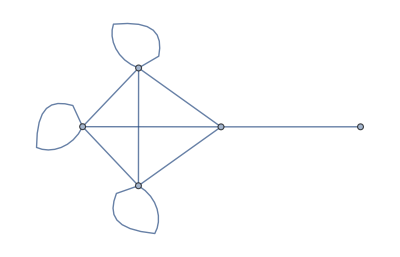

```mathematica
symmetrize[x_]:=Module[{result=x}, Do[
If[result[[i]][[j]] == 1, result[[j]][[i]] =1, ],
{i, 1, Length[result]}, {j, 1, Length[result]}];
Return[result]]
symmetricAdjMatrix = symmetrize[adjMatrix] ;
StringForm["Is the new relation (with symmtric closure)? ``", symmetric[symmetricAdjMatrix]]
AdjacencyGraph[symmetricAdjMatrix]
```

## Computational Exercise 3

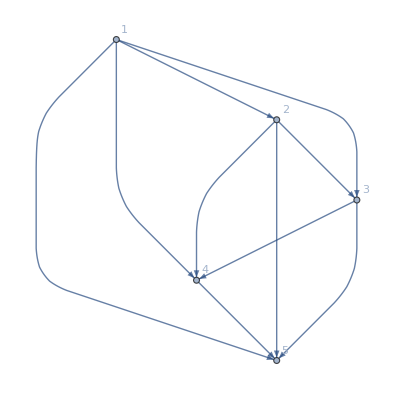

SparseArray[<10>, {5, 5}]

< | 1 | 2 | 3 | 4 | 5
1 | 0 | 1 | 1 | 1 | 1
2 | 0 | 0 | 1 | 1 | 1
3 | 0 | 0 | 0 | 1 | 1
4 | 0 | 0 | 0 | 0 | 1
5 | 0 | 0 | 0 | 0 | 0

```mathematica
g = RelationGraph[Less,Range[1, 5]]
a = AdjacencyMatrix[g]
a//Labeled["<", TableForm[#, TableHeadings->{{1, 2, 3, 4, 5}, {1, 2, 3, 4, 5}}]]&
```

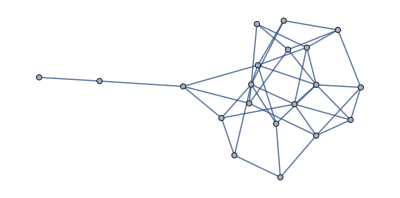

```mathematica
g0 = RandomGraph[BernoulliGraphDistribution[20,0.2]]
```

```mathematica
d = VertexDegree[g0]
```

{3,4,5,4,8,6,7,6,4,4,4,3,5,4,4,3,1,2,4,3}

```mathematica
Tally[d]
```

{{3,4},{4,8},{5,2},{8,1},{6,2},{7,1},{1,1},{2,1}}

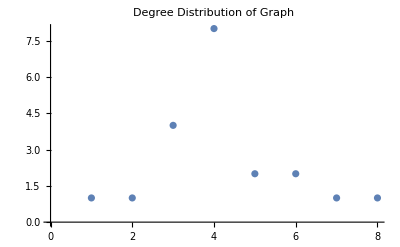

```mathematica
ListPlot[Tally[d], PlotLabel->"Degree Distribution of Graph"]
```

## Computational Exercise 4

```mathematica
adjList = {1->1, 1->3, 2->1, 2->2, 2->3, 3->2,3->3, 3->5, 4->1,4->2,4->3, 4->4, 5->1,5->2,5->3,5->5}
g1 = Graph[adjList]
AdjacencyMatrix[g1]//MatrixForm
```

{1->1,1->3,2->1,2->2,2->3,3->2,3->3,3->5,4->1,4->2,4->3,4->4,5->1,5->2,5->3,5->5}

-Graphics-

(1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1)